```mathematica
poems = Import["C:\\Users\\Stephen\\Desktop\\word-cloud\\fetch\\poems.txt"];
fiction = Import["C:\\Users\\Stephen\\Desktop\\word-cloud\\fetch\\fiction.txt"];
combined = Import["C:\\Users\\Stephen\\Desktop\\word-cloud\\fetch\\combined.txt"];
```

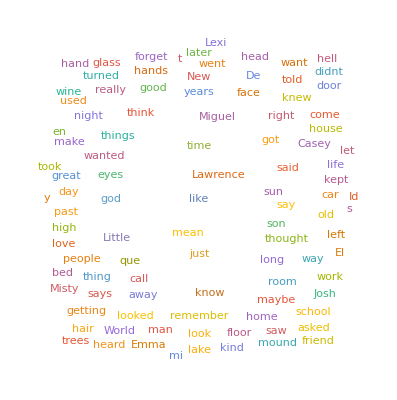

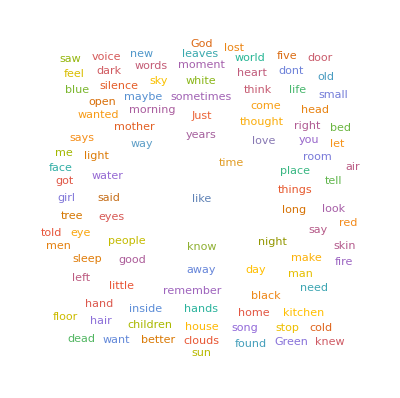

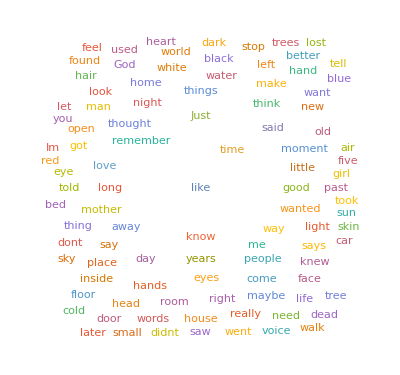

```mathematica
WordCloud[DeleteStopwords[fiction]]
WordCloud[DeleteStopwords[poems]]
WordCloud[DeleteStopwords[combined]]
```